# Mouse Tracking Tooltip Demonstration

## The goal is to create a graph that operates like this:

https://www.washingtonpost.com/graphics/2020/world/corona-simulator/

## Step 1 - The data

```mathematica
jan={1,1,2,2,5,5,5,5,5,6};
feb={8,8,11,11,12,12,12,12,12,12,13,13,15,15,15,15,15,15,15,15,35,35,35,53,53,59,60,62,70};
mar={76,101,122,153,221,278,417,537,605,959,1281,1663,2179};
data=Flatten[{jan,feb,mar}];
days=DateRange["22-Jan-2020","13-April-2020"];
```

## Step 2 - Vanilla ListPlot

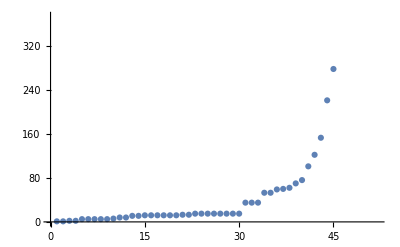

```mathematica
ListPlot@data
```

## Step 3 - Line plot, Filled, Line darker coloring

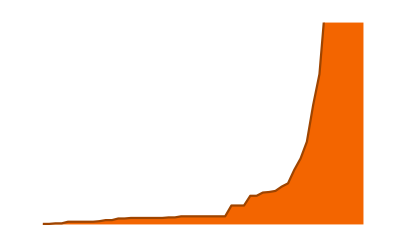

```mathematica
color=LABColor[.6,.5,1];
dcolor=Darker[color];
plotopts={Axes->False,
PlotStyle->dcolor,Joined->True, Filling->Axis, FillingStyle->color};
ListPlot[data, plotopts]
```

## Step 4 - Axes

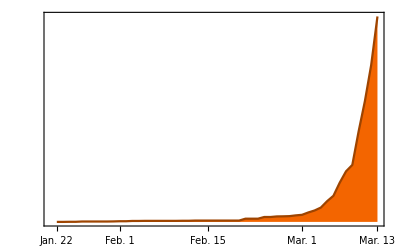

```mathematica
color=LABColor[.6,.5,1];
dcolor=Darker[color];
frameticks={{1,"Jan. 22"},{11,"Feb. 1"},{25,"Feb. 15"},{40,"Mar. 1"},{52,"Mar. 13"}};
plotopts={Axes->False,PlotRange->{1,Max@data},
PlotStyle->dcolor,Joined->True, Filling->Axis, FillingStyle->color,Frame->{{False,False},{True,False}},FrameTicks->{{None,None},{frameticks,None}}};
ListPlot[data,plotopts]
```

## Step 5 - Overlays

```mathematica
line1=ConstantArray[1000,Length@data];
line2=ConstantArray[2000,Length@data];
```

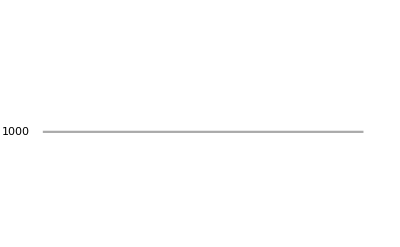
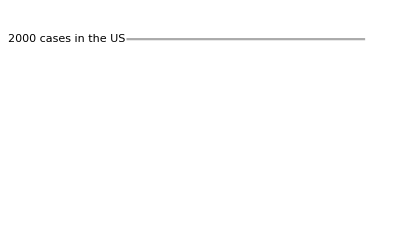
-Graphics--Graphics--Graphics-

```mathematica
p1=ListPlot[data,plotopts];
lineopts={Axes->False,PlotRange->{1,Max@data},
PlotStyle->Lighter@Gray,Joined->True, Filling->None,Frame->{{False,False},{False,False}}};
p2opts=Flatten@{lineopts,{PlotLabels->Placed["1000",Before]}};
p2=ListPlot[line1,p2opts];
p3opts=
Flatten@{lineopts,{PlotLabels->Placed["2000 cases in the US",Before]}};
p3=ListPlot[line2,p3opts];
Overlay[{p1,p2,p3}]
```

## Step 6 - Tracking Labels

For a few minutes, lets return to a simpler plot just to get the labels and point highlighting. 
Here we are going to implement five features:
· The focus follows the mouse movement
· The initial focus is at the maximum peak point
· There is a numeric label that follows the focus point
. There is an x-axis label (date) that follows the focus x-axis position
· The numerals use comma-separated thousands
· The peak point has the units “cases” added to the label
· The numeric font has a white backround
. [ no vertical Axis, The plot line is darker,

```mathematica
ClearAll[idata,indexedData];
toTxt[n_]:=Style[NumberForm[n,DigitBlock->3],Background->White];
dayLabel[date_]:=DateValue[date,"MonthNameShort",String]<>" "<>DateValue[date,"Day",String];
focusPt[j_,pval_,gap_]:={
PointSize[0.02],
PlotRangeClipping->False,
Text[toTxt@pval,{j,pval}+{2,gap}],
Point[{j,pval}],
Text[dayLabel[days⟦j⟧],{j,-160}],
Line[{{j,0},{j,-100}}]
};
indexedData=MapIndexed[{#2[[1]],#1}&,data];
idata=%;
xpad=5;
ypad=0.1*Max@data;
gap=100;
plotopts={Axes->False,Joined->True, Filling->Axis,PlotRangeClipping->False,PlotRange->{{-xpad,Length@data+xpad},{-ypad,Max@data+ypad}}};
Manipulate[
Module[{pval=idata⟦j,2⟧},
DiscretePlot[idata⟦i,2⟧,{i,Length@data},Evaluate@plotopts,Epilog->focusPt[j,pval,gap]]],{j,1,Length@data,1}]
```

## Step 8 - Mouse Tracking

The basic idea is to use MousePosition with EventHandler to feed a Dynamic DiscretePlot with changing Epilog or PlotMarkers based on mouse position.

```mathematica
ClearAll[idata,indexedData];
indexedData=MapIndexed[{#2[[1]],#1}&,data];
idata=%;
pad=100;
plotopts={Axes->False,Joined->True, Filling->Axis,PlotRange->{-pad,Max@data+pad}};

DynamicModule[{p=None,j=10,pval=idata⟦10,2⟧},
EventHandler[Dynamic@DiscretePlot[
idata⟦i,2⟧,{i,Length@data},Evaluate@plotopts,Epilog->{PointSize[0.025],Text[NumberForm[pval,DigitBlock->3],{j,pval}+{2,pad}],Point[{j,pval}]}],
"MouseMoved":>(
p=IntegerPart@MousePosition["Graphics"]⟦1⟧;
If[p>0&&p≤Length@data,j=p; pval=idata⟦j,2⟧]
)]]
```